# Ph3 Set 3

## Jacob Snyder

## 4/4/19

```mathematica
data=Import["~/Downloads/getwfm.isf"]
data2=Most[data]
```

{{-0.01,0.028},{-0.009998,0.032},{-0.009996,0.036},{-0.009994,0.04},{-0.009992,0.056},{-0.00999,0.064},{-0.009988,0.064},{-0.009986,0.072},9985,{0.009986,-0.012},{0.009988,-0.012},{0.00999,0},{0.009992,0},{0.009994,0.008},{0.009996,0.02},{0.009998,0.024},{}}
 |  |  |  |

{{-0.01,0.028},{-0.009998,0.032},{-0.009996,0.036},{-0.009994,0.04},{-0.009992,0.056},{-0.00999,0.064},{-0.009988,0.064},{-0.009986,0.072},9985,{0.009986,-0.012},{0.009988,-0.012},{0.00999,0},{0.009992,0},{0.009994,0.008},{0.009996,0.02},{0.009998,0.024}}
 |  |  |  |

```mathematica
data2=Table[data[[i]],{i,Length[data]-1}]
```

{{-0.01,0.028},{-0.009998,0.032},{-0.009996,0.036},{-0.009994,0.04},{-0.009992,0.056},{-0.00999,0.064},{-0.009988,0.064},{-0.009986,0.072},9985,{0.009986,-0.012},{0.009988,-0.012},{0.00999,0},{0.009992,0},{0.009994,0.008},{0.009996,0.02},{0.009998,0.024}}
 |  |  |  |

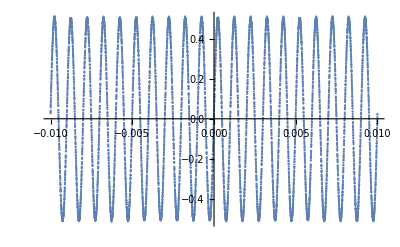

```mathematica
ListPlot[data2]
```

```mathematica
shortdata=Table[data2[[i]],{i,10}];
TableForm[shortdata]
```

-0.01 | 0.028
-0.009998 | 0.032
-0.009996 | 0.036
-0.009994 | 0.04
-0.009992 | 0.056
-0.00999 | 0.064
-0.009988 | 0.064
-0.009986 | 0.072
-0.009984 | 0.08
-0.009982 | 0.088

```mathematica
times=Table[data2[[i,1]],{i,Length[data2]}]
```

{-0.01,-0.009998,-0.009996,-0.009994,-0.009992,-0.00999,-0.009988,-0.009986,-0.009984,-0.009982,-0.00998,-0.009978,-0.009976,-0.009974,-0.009972,9970,0.00997,0.009972,0.009974,0.009976,0.009978,0.00998,0.009982,0.009984,0.009986,0.009988,0.00999,0.009992,0.009994,0.009996,0.009998}
 |  |  |  |

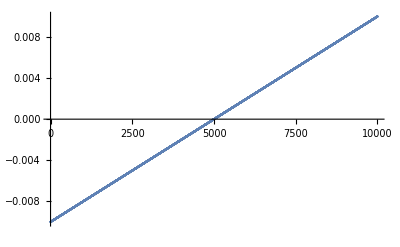

```mathematica
ListPlot[times]
```

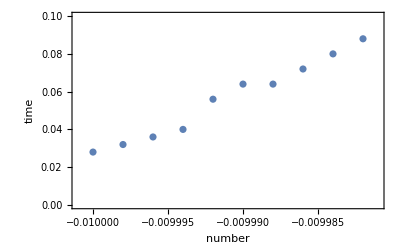

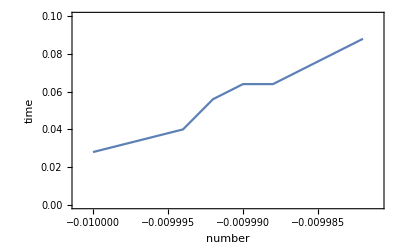

```mathematica
ListPlot[shortdata,PlotRange->{{-0.010001,-0.009981},{0,0.1}},Frame->True,FrameLabel->{"number","time"}]
ListPlot[shortdata,PlotRange->{{-0.010001,-0.009981},{0,0.1}},Frame->True,FrameLabel->{"number","time"},Joined->True]
```

```mathematica
data=Drop@Import["http://pmaweb.caltech.edu/~phy003/labs/Data1.txt","TSV"]
```

{{X,Y},{0.,3.4039},{0.5,3.9881},{1.,4.2004},{1.5,5.0291},{2.,5.188},{2.5,5.3914},{3.,5.7904},{3.5,5.4771},{4.,5.784},{4.5,5.9271},{5.,7.1422},{5.5,7.1213},{6.,6.8499},{6.5,7.936},{7.,8.3686},{7.5,8.2178},{8.,8.8891},{8.5,8.8176},{9.,8.8702},{9.5,9.8769},{10.,9.7354}}

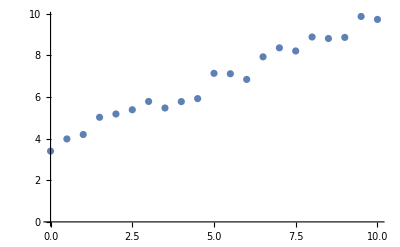

```mathematica
ListPlot[data]
```

```mathematica
Needs["ErrorBarPlots`"]
```

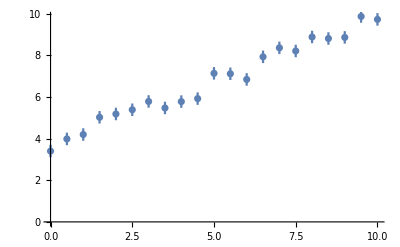

```mathematica
ErrorListPlot[Table[{data[[i]],ErrorBar[0.3]},{i,Length[data]}]]
```